```mathematica
k[n_]:= (n Pi)/L + ϵ/L+ϵ^2/L+ ϵ^3/L+ϵ^4/L
j[n_]:= (n Pi)/(2L) + ϵ/L+ϵ^2/L+ ϵ^3/L+ϵ^4/L
An[n_]:= An0 + ϵ An1 + ϵ^2 An2 +  ϵ^3 An3 
A0[n_]:=A00 + ϵ A01 + ϵ^2 A02 +  ϵ^3 A03 
Cn[n_]:=  Cn0 + ϵ Cn1 + ϵ^2 Cn2 +  ϵ^3 Cn3 
(*λ[y_] := HeavisideTheta[-y]ρ1 κ1 + HeavisideTheta[y]ρ2 κ2*)
λ[y_] := f1[y]
T4[x_, y_, n_]:= Cos[k[n] y](An[n]Sinh[k[n]x] + (TS4 ϵ^2)/(π^2 n^2)2 Cos[π n]Exp[-k[n]x]) + λ[y]Sin[j[n]y] Cn[n]Sinh[j[n]x]
```

Check surface

```mathematica
Simplify[Sum[T4[0,0,n],{n,1,∞}] ]
```

-(TS4 ϵ^2)/6

```mathematica
Series[D[T4[x,y,1],y]/.y->L,{ϵ,0,2}];
```

Cn0 (-κ1 ρ1 DiracDelta[L]+κ2 ρ2 DiracDelta[L]) Sinh[(π x)/(2 L)]+(-(Cn0 π (κ1 ρ1 HeavisideTheta[-L]+κ2 ρ2 HeavisideTheta[L]) Sinh[(π x)/(2 L)])/(2 L)+(-κ1 ρ1 DiracDelta[L]+κ2 ρ2 DiracDelta[L]) ((Cn0 x Cosh[(π x)/(2 L)])/L+Cn1 Sinh[(π x)/(2 L)])+(An0 π Sinh[(π x)/L])/L) ϵ+((κ1 ρ1 HeavisideTheta[-L]+κ2 ρ2 HeavisideTheta[L]) (-(Cn0 π x Cosh[(π x)/(2 L)])/(2 L^2)+(-Cn0/L-(Cn0 π)/(2 L)-(Cn1 π)/(2 L)) Sinh[(π x)/(2 L)])+(-κ1 ρ1 DiracDelta[L]+κ2 ρ2 DiracDelta[L]) ((Cn1 x Cosh[(π x)/(2 L)])/L+(-Cn0/2+Cn2) Sinh[(π x)/(2 L)]+Cn0 ((x Cosh[(π x)/(2 L)])/L+(x^2 Sinh[(π x)/(2 L)])/(2 L^2)))+(An0 π x Cosh[(π x)/L]+An0 L Sinh[(π x)/L]+An0 L π Sinh[(π x)/L]+An1 L π Sinh[(π x)/L])/L^2) ϵ^2+O[ϵ]^3

Cn0 (-κ1 ρ1 DiracDelta[L]+κ2 ρ2 DiracDelta[L]) Sinh[(π x)/(2 L)]+(-(Cn0 π (κ1 ρ1 HeavisideTheta[-L]+κ2 ρ2 HeavisideTheta[L]) Sinh[(π x)/(2 L)])/(2 L)+(-κ1 ρ1 DiracDelta[L]+κ2 ρ2 DiracDelta[L]) ((Cn0 x Cosh[(π x)/(2 L)])/L+Cn1 Sinh[(π x)/(2 L)])+(An0 π Sinh[(π x)/L])/L) ϵ+O[ϵ]^2

```mathematica
TS4S[x_,y_,N_] :=Cos[k[0] y](A0[0]Sinh[k[0]x ] + TS4 Exp[-k[0]x ](1+ϵ^2/6)) + T4[x,y,N]
```

```mathematica
Series[TS4S[x,y,nn],{ϵ,0,1}]
```

(TS4+Cn0 (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)] Sinh[(nn π x)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(nn π x)/L])+((A00 x-TS4 x)/L+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) ((Cn0 x Cosh[(nn π x)/(2 L)] Sin[(nn π y)/(2 L)])/L+((Cn0 y Cos[(nn π y)/(2 L)])/L+Cn1 Sin[(nn π y)/(2 L)]) Sinh[(nn π x)/(2 L)])-(An0 y Sin[(nn π y)/L] Sinh[(nn π x)/L])/L+Cos[(nn π y)/L] ((An0 x Cosh[(nn π x)/L])/L+An1 Sinh[(nn π x)/L])) ϵ+O[ϵ]^2

```mathematica
Normal[Series[TS4S[c0,y,nn]- c1(Cos[π y/L] + λ[y]Sin[π y/(2L)])D[TS4S[x,y,nn],x]/.x->c0,{ϵ,0,2}]]
```

```mathematica
%15/.{An1->0, An0->0}/.(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y])->0
```

TS4+ϵ ((A00 c0-c0 TS4)/L-(c1 (A00-TS4) Cos[(π y)/L])/L)+ϵ^2 ((6 A00 c0 L+6 A01 c0 L+3 c0^2 TS4-6 c0 L TS4+L^2 TS4-3 TS4 y^2)/(6 L^2)+c1 Cos[(π y)/L] (-(A00+A01)/L-((c0-L) TS4)/L^2-Cos[(nn π y)/L] (-(2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(L nn π)+(An2 nn π Cosh[(c0 nn π)/L])/L))+Cos[(nn π y)/L] ((2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(nn^2 π^2)+An2 Sinh[(c0 nn π)/L]))

```mathematica
(6 A00 c0 L+6 A01 c0 L+3 c0^2 TS4-6 c0 L TS4+L^2 TS4-3 TS4 y^2)/(6 L^2)+c1 Cos[(π y)/L] (-(A00+A01)/L-((c0-L) TS4)/L^2-Cos[(nn π y)/L] (-(2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(L nn π)+(An2 nn π Cosh[(c0 nn π)/L])/L))+Cos[(nn π y)/L] ((2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(nn^2 π^2)+An2 Sinh[(c0 nn π)/L])
```

(6 A00 c0 L+6 A01 c0 L+3 c0^2 TS4-6 c0 L TS4+L^2 TS4-3 TS4 y^2)/(6 L^2)+c1 Cos[(π y)/L] (-(A00+A01)/L-((c0-L) TS4)/L^2-Cos[(nn π y)/L] (-(2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(L nn π)+(An2 nn π Cosh[(c0 nn π)/L])/L))+Cos[(nn π y)/L] ((2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(nn^2 π^2)+An2 Sinh[(c0 nn π)/L])

```mathematica
%18/.A00->TS4
```

(6 A01 c0 L+3 c0^2 TS4+L^2 TS4-3 TS4 y^2)/(6 L^2)+c1 Cos[(π y)/L] (-((c0-L) TS4)/L^2-(A01+TS4)/L-Cos[(nn π y)/L] (-(2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(L nn π)+(An2 nn π Cosh[(c0 nn π)/L])/L))+Cos[(nn π y)/L] ((2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(nn^2 π^2)+An2 Sinh[(c0 nn π)/L])

```mathematica
Integrate[%19 Cos[nn π y/L],{y,-L,L}]
```

```mathematica
-(L TS4 (2 nn π Cos[nn π]))/(nn^3 π^3)+(ⅇ^(-(c0 nn π)/L) L TS4 Cos[nn π] (2 nn π))/(nn^3 π^3)+An2 (L) Sinh[(c0 nn π)/L]
```

-(2 L TS4 Cos[nn π])/(nn^2 π^2)+(2 ⅇ^(-(c0 nn π)/L) L TS4 Cos[nn π])/(nn^2 π^2)+An2 L Sinh[(c0 nn π)/L]

```mathematica
Solve[%21==0, An2]
```

{{An2→(2 ⅇ^(-(c0 nn π)/L) (-1+ⅇ^((c0 nn π)/L)) TS4 Cos[nn π] Csch[(c0 nn π)/L])/(nn^2 π^2)}}

```mathematica
TeXForm[(2 ⅇ^(-(c0 nn π)/L) (-1+ⅇ^((c0 nn π)/L)) TS4 Cos[nn π] Csch[(c0 nn π)/L])/(nn^2 π^2)]
```

\frac{2 \text{TS4} \cos (\pi  \text{nn}) e^{-\frac{\pi  \text{c0} \text{nn}}{L}} \left(e^{\frac{\pi  \text{c0} \text{nn}}{L}}-1\right) \text{csch}\left(\frac{\pi 
   \text{c0} \text{nn}}{L}\right)}{\pi ^2 \text{nn}^2}

```mathematica
FullSimplify[%160]
```

(TS4-1/(2 L)c1 nn π (Cos[(π y)/L]+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(π y)/(2 L)]) (2 An0 Cos[(nn π y)/L] Cosh[(c0 nn π)/L]+Cn0 Cosh[(c0 nn π)/(2 L)] (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)])+Cn0 (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L])+O[ϵ]^1

```mathematica
Expand[%160]
```

(TS4+c1 (Cos[(π y)/L]+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(π y)/(2 L)]) (-(An0 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L-(Cn0 nn π Cosh[(c0 nn π)/(2 L)] (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)])/(2 L))+Cn0 (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L])+O[ϵ]^1

```mathematica
Integrate[Cos[m π y/L]Sin[n π y/(2L)],{y,-L,0}]
Integrate[Cos[m π y/L]Sin[n π y/(2L)],{y,0,L}]
```

(2 L (n-n Cos[m π] Cos[(n π)/2]-2 m Sin[m π] Sin[(n π)/2]))/((4 m^2-n^2) π)

(2 L (-n+n Cos[m π] Cos[(n π)/2]+2 m Sin[m π] Sin[(n π)/2]))/((4 m^2-n^2) π)

```mathematica
(TS4+c1 (Cos[(π y)/L]+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(π y)/(2 L)]) (-(An0 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L-(Cn0 nn π Cosh[(c0 nn π)/(2 L)] (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)])/(2 L))+Cn0 (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L])+O[ϵ]^1
```

(TS4+c1 (Cos[(π y)/L]+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(π y)/(2 L)]) (-(An0 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L-(Cn0 nn π Cosh[(c0 nn π)/(2 L)] (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)])/(2 L))+Cn0 (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L])+O[ϵ]^1

```mathematica
Normal[%167]/.(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y])->0
```

TS4-(An0 c1 nn π Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]

```mathematica
Integrate[%175Cos[nn π y/L],{y,-L,L}]
```

```mathematica
(L (An0 (2 nn π) Sinh[(c0 nn π)/L]))/(2 nn π)
```

An0 L Sinh[(c0 nn π)/L]

```mathematica
TeXForm[An0 L Sinh[(c0 nn π)/L]]
```

\text{An0} L \sinh \left(\frac{\pi  \text{c0} \text{nn}}{L}\right)

```mathematica
-(c0 TS4)/L+c1 Cos[(π y)/L] (TS4/L-(An1 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L)+An1 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]
```

-(c0 TS4)/L+c1 Cos[(π y)/L] (TS4/L-(An1 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L)+An1 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]

```mathematica
Integrate[%187Cos[nn π y/L],{y,-L,L}]/.{Sin[nn π] ->0, Sin[2 nn π]->0}
```

An1 L Sinh[(c0 nn π)/L]

```mathematica
(3 c0^2 TS4-6 c0 L TS4+L^2 TS4-3 TS4 y^2)/(6 L^2)+c1 Cos[(π y)/L] (-((c0-L) TS4)/L^2-Cos[(nn π y)/L] (-(2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(L nn π)+(An2 nn π Cosh[(c0 nn π)/L])/L))+Cos[(nn π y)/L] ((2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(nn^2 π^2)+An2 Sinh[(c0 nn π)/L])
```

(3 c0^2 TS4-6 c0 L TS4+L^2 TS4-3 TS4 y^2)/(6 L^2)+c1 Cos[(π y)/L] (-((c0-L) TS4)/L^2-Cos[(nn π y)/L] (-(2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(L nn π)+(An2 nn π Cosh[(c0 nn π)/L])/L))+Cos[(nn π y)/L] ((2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(nn^2 π^2)+An2 Sinh[(c0 nn π)/L])

```mathematica
Integrate[%193Cos[nn π y/L],{y,-L,L}]/.{Sin[nn π] ->0, Sin[2 nn π]->0}
```

-(2 L TS4 Cos[nn π])/(nn^2 π^2)+(2 ⅇ^(-(c0 nn π)/L) L TS4 Cos[nn π])/(nn^2 π^2)+An2 L Sinh[(c0 nn π)/L]

```mathematica
Solve[%196 ==0, An2]
```

{{An2→(2 ⅇ^(-(c0 nn π)/L) (-1+ⅇ^((c0 nn π)/L)) TS4 Cos[nn π] Csch[(c0 nn π)/L])/(nn^2 π^2)}}

```mathematica
TeXForm[(2 ⅇ^(-(c0 nn π)/L) (-1+ⅇ^((c0 nn π)/L)) TS4 Cos[nn π] Csch[(c0 nn π)/L])/(nn^2 π^2)]
```

\frac{2 \text{TS4} \cos (\pi  \text{nn}) e^{-\frac{\pi  \text{c0} \text{nn}}{L}}
   \left(e^{\frac{\pi  \text{c0} \text{nn}}{L}}-1\right) \text{csch}\left(\frac{\pi 
   \text{c0} \text{nn}}{L}\right)}{\pi ^2 \text{nn}^2}

```mathematica
Series[Cos[n π y/L + ϕ1 ϵ/L + ϕ2 ϵ^2/L+ϕ3 ϵ^3/L],{ϵ,0,2}]
```

Cos[(n π y)/L]-(ϕ1 Sin[(n π y)/L] ϵ)/L+(-(ϕ1^2 Cos[(n π y)/L])/(2 L^2)-(ϕ2 Sin[(n π y)/L])/L) ϵ^2+O[ϵ]^3

```mathematica
Series[D[Cos[n π y/L + ϕ1 ϵ/L + ϕ2 ϵ^2/L+ϕ3 ϵ^3/L], y]/.y->L, {ϵ,0,2}]/.Sin[n π]->0
```

-(n π ϕ1 Cos[n π] ϵ)/L^2-(n π ϕ2 Cos[n π] ϵ^2)/L^2+O[ϵ]^3

```mathematica
Series[D[Sin[n π y/(2L) + ϕ1 ϵ/L + ϕ2 ϵ^2/L+ϕ3 ϵ^3/L], y]/.y->L, {ϵ,0,2}]/.Sin[n π]->0
```

(n π Cos[(n π)/2])/(2 L)-((n π ϕ1 Sin[(n π)/2]) ϵ)/(2 L^2)-((n π (ϕ1^2 Cos[(n π)/2]+2 L ϕ2 Sin[(n π)/2])) ϵ^2)/(4 L^3)+O[ϵ]^3

order 0

```mathematica
TS4S[x_,y_,N_] :=Cos[k[0] y](A0[0]Sinh[k[0]x ] + TS4 Exp[-k[0]x ](1+ϵ^2/6)) + T4[x,y,N]
```

```mathematica
Normal[Series[TS4S[c0,y,nn]+ c1(Cos[π y/L] + λ[y]Sin[π y/(2L)])D[TS4S[x,y,nn],x]/.x->c0  ,{ϵ,0,0}]]
```

TS4+c1 (Cos[(π y)/L]+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(π y)/(2 L)]) ((An0 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(Cn0 nn π Cosh[(c0 nn π)/(2 L)] (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)])/(2 L))+Cn0 (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]

```mathematica
Integrate[%37 Cos[nn π y/L],{y,-L,L}]/.{Sin[2 nn π]->0, Sin[ nn π]->0}
```

An0 L Sinh[(c0 nn π)/L]

Order 0 attempt 2

```mathematica
Normal[Series[TS4S[c0,y,nn]+ c1(Cos[π y/L] + λ[y]Sin[π y/(2L)])D[TS4S[x,y,nn],x]/.x->c0  ,{ϵ,0,0}]]
```

TS4+c1 (Cos[(π y)/L]+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(π y)/(2 L)]) ((An0 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(Cn0 nn π Cosh[(c0 nn π)/(2 L)] (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)])/(2 L))+Cn0 (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]

```mathematica
Integrate[ Sin[ (2π y)/(2L)]Sin[(2 π y)/(2 L)],{y,-L,L}]
```

L

```mathematica
TS4+c1 (Cos[(π y)/L]+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(π y)/(2 L)]) ((An0 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(Cn0 nn π Cosh[(c0 nn π)/(2 L)] (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)])/(2 L))+Cn0 (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]
```

TS4+c1 (Cos[(π y)/L]+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(π y)/(2 L)]) ((An0 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(Cn0 nn π Cosh[(c0 nn π)/(2 L)] (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)])/(2 L))+Cn0 (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]

```mathematica
TS4+c1 (Cos[(π y)/L]+f1[y] Sin[(π y)/(2 L)]) ((An0 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(Cn0 nn π Cosh[(c0 nn π)/(2 L)] f1[y] Sin[(nn π y)/(2 L)])/(2 L))+Cn0 f1[y] Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]
```

TS4+c1 (Cos[(π y)/L]+f1[y] Sin[(π y)/(2 L)]) ((An0 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(Cn0 nn π Cosh[(c0 nn π)/(2 L)] f1[y] Sin[(nn π y)/(2 L)])/(2 L))+Cn0 f1[y] Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]

```mathematica
Expand[%79]
```

```mathematica
TS4+(An0 c1 nn π Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(c1 Cn0 nn π Cosh[(c0 nn π)/(2 L)] f1[y]^2 Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/(2 L)+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]
```

```mathematica
Expand[%72]
```

```mathematica
TS4+(An0 c1 nn π Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(c1 Cn0 nn π κ1^2 ρ1^2 Cosh[(c0 nn π)/(2 L)] HeavisideTheta[-y]^2 Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/(2 L)+(c1 Cn0 nn π κ1 κ2 ρ1 ρ2 Cosh[(c0 nn π)/(2 L)] HeavisideTheta[-y] HeavisideTheta[y] Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/L+(c1 Cn0 nn π κ2^2 ρ2^2 Cosh[(c0 nn π)/(2 L)] HeavisideTheta[y]^2 Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/(2 L)+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]
```

TS4+(An0 c1 nn π Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(c1 Cn0 nn π κ1^2 ρ1^2 Cosh[(c0 nn π)/(2 L)] HeavisideTheta[-y]^2 Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/(2 L)+(c1 Cn0 nn π κ1 κ2 ρ1 ρ2 Cosh[(c0 nn π)/(2 L)] HeavisideTheta[-y] HeavisideTheta[y] Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/L+(c1 Cn0 nn π κ2^2 ρ2^2 Cosh[(c0 nn π)/(2 L)] HeavisideTheta[y]^2 Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/(2 L)+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]

```mathematica
%74/.{Cn0->Subscript[C, N]^(0), An0->Subscript[A, n]^(0),κ1->Subscript[κ, 1], κ2->Subscript[κ, 2], ρ1->Subscript[ρ, 1], ρ2->Subscript[ρ, 2], nn->n , c1->Subscript[c, 1], c0->Subscript[c, 0]}
```

TS4+Cos[(n π y)/L] Sinh[(n π c_0)/L]+(n π Cos[(π y)/L] Cos[(n π y)/L] Cosh[(n π c_0)/L] c_1)/L+(n π Cosh[(n π c_0)/(2 L)] HeavisideTheta[-y]^2 Sin[(π y)/(2 L)] Sin[(n π y)/(2 L)] c_1 κ_1^2 ρ_1^2)/(2 L)+(n π Cosh[(n π c_0)/(2 L)] HeavisideTheta[-y] HeavisideTheta[y] Sin[(π y)/(2 L)] Sin[(n π y)/(2 L)] c_1 κ_1 κ_2 ρ_1 ρ_2)/L+(n π Cosh[(n π c_0)/(2 L)] HeavisideTheta[y]^2 Sin[(π y)/(2 L)] Sin[(n π y)/(2 L)] c_1 κ_2^2 ρ_2^2)/(2 L)

```mathematica
Simplify[%75]
```

TS4+Cos[(n π y)/L] Sinh[(n π c_0)/L]+1/(2 L)n π c_1 (2 Cos[(π y)/L] Cos[(n π y)/L] Cosh[(n π c_0)/L]+Cosh[(n π c_0)/(2 L)] HeavisideTheta[-y]^2 Sin[(π y)/(2 L)] Sin[(n π y)/(2 L)] κ_1^2 ρ_1^2+2 Cosh[(n π c_0)/(2 L)] HeavisideTheta[-y] HeavisideTheta[y] Sin[(π y)/(2 L)] Sin[(n π y)/(2 L)] κ_1 κ_2 ρ_1 ρ_2+Cosh[(n π c_0)/(2 L)] HeavisideTheta[y]^2 Sin[(π y)/(2 L)] Sin[(n π y)/(2 L)] κ_2^2 ρ_2^2)

```mathematica
TeXForm[%75]
```

\frac{\pi  c_1 \kappa _1^2 n \rho _1^2 \theta (-y)^2 \sin \left(\frac{\pi  y}{2 L}\right) \cosh \left(\frac{\pi  c_0 n}{2 L}\right) \sin \left(\frac{\pi  n y}{2
   L}\right)}{2 L}+\frac{\pi  c_1 \kappa _1 \kappa _2 n \rho _2 \rho _1 \theta (-y) \theta (y) \sin \left(\frac{\pi  y}{2 L}\right) \cosh \left(\frac{\pi  c_0 n}{2
   L}\right) \sin \left(\frac{\pi  n y}{2 L}\right)}{L}+\frac{\pi  c_1 \kappa _2^2 n \rho _2^2 \theta (y)^2 \sin \left(\frac{\pi  y}{2 L}\right) \cosh \left(\frac{\pi  c_0
   n}{2 L}\right) \sin \left(\frac{\pi  n y}{2 L}\right)}{2 L}+\sinh \left(\frac{\pi  c_0 n}{L}\right) \cos \left(\frac{\pi  n y}{L}\right)+\frac{\pi  c_1 n \cos
   \left(\frac{\pi  y}{L}\right) \cosh \left(\frac{\pi  c_0 n}{L}\right) \cos \left(\frac{\pi  n y}{L}\right)}{L}+\text{TS4}

```mathematica
Integrate[Sin[(π y)/(2 L)]Cos[(nn π y)/L]Cos[nn π y/L],{y,-L,0}] + Integrate[Sin[(π y)/(2 L)]Cos[(nn π y)/L]Cos[nn π y/L],{y,0,L}]
```

0

```mathematica
Integrate[Sin[(nn π y)/(2 L)]Sin[(π y)/(2 L)]Cos[nn π y/L],{y,-L,0}] + Integrate[Sin[(nn π y)/(2 L)]Sin[(π y)/(2 L)]Cos[nn π y/L],{y,0,L}]
```

-(4 L nn Cos[(nn π)/2] (2-6 nn^2+3 (-1+nn^2) Cos[nn π]))/((1-10 nn^2+9 nn^4) π)

TS4+(c1 Cn0 nn π Cosh[(c0 nn π)/(2 L)] (κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) (Cos[(π y)/L]+(κ1 ρ1 HeavisideTheta[-y]+κ2 ρ2 HeavisideTheta[y]) Sin[(π y)/(2 L)]) Sin[(nn π y)/(2 L)])/(2 L)+An0 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]

```mathematica
%64/.{Cn0->Subscript[C, N]^(0), An0->Subscript[A, n]^(0),κ1->Subscript[κ, 1], κ2->Subscript[κ, 2], ρ1->Subscript[ρ, 1], ρ2->Subscript[ρ, 2], nn->n , c1->Subscript[c, 1], c0->Subscript[c, 0]}
```

```mathematica
Normal[Series[TS4S[c0,y,nn]+ c1(Cos[π y/L] + λ[y]Sin[π y/(2L)])D[TS4S[x,y,nn],x]/.x->c0  ,{ϵ,0,1}]]/.{An0->0, Cn0->0, A00->TS4}
```

TS4+ϵ (c1 (Cos[(π y)/L]+f1[y] Sin[(π y)/(2 L)]) ((An1 nn π Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(Cn1 nn π Cosh[(c0 nn π)/(2 L)] f1[y] Sin[(nn π y)/(2 L)])/(2 L))+Cn1 f1[y] Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+An1 Cos[(nn π y)/L] Sinh[(c0 nn π)/L])

```mathematica
Expand[%97]
```

```mathematica
TS4+(An1 c1 nn π ϵ Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(c1 Cn1 nn π ϵ Cosh[(c0 nn π)/(2 L)] f1[y]^2 Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/(2 L)+An1 ϵ Cos[(nn π y)/L] Sinh[(c0 nn π)/L]
```

```mathematica
(An1 c1 nn π ϵ Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(c1 Cn1 nn π ϵ Cosh[(c0 nn π)/(2 L)] f1[y]^2 Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/(2 L)+An1 ϵ Cos[(nn π y)/L] Sinh[(c0 nn π)/L]
```

This is the order 1 with the sine cos terms cut out

```mathematica
Integrate[Cos[(π y)/L] Cos[(2π y)/L] Cos[2 π y/L],{y,-L,L}]
```

0

order 2

```mathematica
Normal[Series[TS4S[c0,y,nn]+ c1(Cos[π y/L] + λ[y]Sin[π y/(2L)])D[TS4S[x,y,nn],x]/.x->c0  ,{ϵ,0,2}]]/.{An0->0, Cn0->0,An1->0, Cn1->0, A00->TS4}
```

```mathematica
ϵ^2 ((6 A01 c0 L+3 c0^2 TS4+L^2 TS4-3 TS4 y^2)/(6 L^2)+c1 (Cos[(π y)/L]+f1[y] Sin[(π y)/(2 L)]) (((c0-L) TS4)/L^2+(A01+TS4)/L+Cos[(nn π y)/L] (-(2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(L nn π)+(An2 nn π Cosh[(c0 nn π)/L])/L)+(Cn2 nn π Cosh[(c0 nn π)/(2 L)] f1[y] Sin[(nn π y)/(2 L)])/(2 L))+Cn2 f1[y] Sin[(nn π y)/(2 L)] Sinh[(c0 nn π)/(2 L)]+Cos[(nn π y)/L] ((2 ⅇ^(-(c0 nn π)/L) TS4 Cos[nn π])/(nn^2 π^2)+An2 Sinh[(c0 nn π)/L]))
```

```mathematica
Expand[%107]
```

```mathematica
(A01 c0 ϵ^2)/L+(TS4 ϵ^2)/6+(c0^2 TS4 ϵ^2)/(2 L^2)-(TS4 y^2 ϵ^2)/(2 L^2)+(A01 c1 ϵ^2 Cos[(π y)/L])/L+(c0 c1 TS4 ϵ^2 Cos[(π y)/L])/L^2+(2 ⅇ^(-(c0 nn π)/L) TS4 ϵ^2 Cos[nn π] Cos[(nn π y)/L])/(nn^2 π^2)-(2 c1 ⅇ^(-(c0 nn π)/L) TS4 ϵ^2 Cos[nn π] Cos[(π y)/L] Cos[(nn π y)/L])/(L nn π)+(An2 c1 nn π ϵ^2 Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+(c1 Cn2 nn π ϵ^2 Cosh[(c0 nn π)/(2 L)] f1[y]^2 Sin[(π y)/(2 L)] Sin[(nn π y)/(2 L)])/(2 L)+An2 ϵ^2 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]
```

```mathematica
(A01 c0 ϵ^2)/L+(TS4 ϵ^2)/6+(c0^2 TS4 ϵ^2)/(2 L^2)-(TS4 y^2 ϵ^2)/(2 L^2)+(A01 c1 ϵ^2 Cos[(π y)/L])/L+(c0 c1 TS4 ϵ^2 Cos[(π y)/L])/L^2+(2 ⅇ^(-(c0 nn π)/L) TS4 ϵ^2 Cos[nn π] Cos[(nn π y)/L])/(nn^2 π^2)-(2 c1 ⅇ^(-(c0 nn π)/L) TS4 ϵ^2 Cos[nn π] Cos[(π y)/L] Cos[(nn π y)/L])/(L nn π)+(An2 c1 nn π ϵ^2 Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+An2 ϵ^2 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]
```

(A01 c0 ϵ^2)/L+(TS4 ϵ^2)/6+(c0^2 TS4 ϵ^2)/(2 L^2)-(TS4 y^2 ϵ^2)/(2 L^2)+(A01 c1 ϵ^2 Cos[(π y)/L])/L+(c0 c1 TS4 ϵ^2 Cos[(π y)/L])/L^2+(2 ⅇ^(-(c0 nn π)/L) TS4 ϵ^2 Cos[nn π] Cos[(nn π y)/L])/(nn^2 π^2)-(2 c1 ⅇ^(-(c0 nn π)/L) TS4 ϵ^2 Cos[nn π] Cos[(π y)/L] Cos[(nn π y)/L])/(L nn π)+(An2 c1 nn π ϵ^2 Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L+An2 ϵ^2 Cos[(nn π y)/L] Sinh[(c0 nn π)/L]

```mathematica
Integrate[%109 Cos[nn y π/L],{y,-L,L}]
```

1/(6 L^2 nn^2 π^2)ⅇ^(-(c0 nn π)/L) ϵ^2 (-3 An2 L^3 nn^2 π^2+3 An2 ⅇ^((2 c0 nn π)/L) L^3 nn^2 π^2+12 L^3 TS4 Cos[nn π]-12 ⅇ^((c0 nn π)/L) L^3 TS4 Cos[nn π]+12 A01 c0 ⅇ^((c0 nn π)/L) L^2 nn π Sin[nn π]-(6 A01 c1 ⅇ^((c0 nn π)/L) L^2 nn^2 π Sin[nn π])/(-1+nn)-(6 A01 c1 ⅇ^((c0 nn π)/L) L^2 nn^2 π Sin[nn π])/(1+nn)+(12 ⅇ^((c0 nn π)/L) L^3 TS4 Sin[nn π])/(nn π)+6 c0^2 ⅇ^((c0 nn π)/L) L nn π TS4 Sin[nn π]-4 ⅇ^((c0 nn π)/L) L^3 nn π TS4 Sin[nn π]-(6 c0 c1 ⅇ^((c0 nn π)/L) L nn^2 π TS4 Sin[nn π])/(-1+nn)-(6 c0 c1 ⅇ^((c0 nn π)/L) L nn^2 π TS4 Sin[nn π])/(1+nn)-3/2 An2 L^3 nn π Sin[2 nn π]+3/2 An2 ⅇ^((2 c0 nn π)/L) L^3 nn π Sin[2 nn π]-(3 An2 c1 L^2 nn^3 π^2 Sin[2 nn π])/(2 (-1+2 nn))-(3 An2 c1 ⅇ^((2 c0 nn π)/L) L^2 nn^3 π^2 Sin[2 nn π])/(2 (-1+2 nn))-(3 An2 c1 L^2 nn^3 π^2 Sin[2 nn π])/(2 (1+2 nn))-(3 An2 c1 ⅇ^((2 c0 nn π)/L) L^2 nn^3 π^2 Sin[2 nn π])/(2 (1+2 nn))+(6 c1 L^2 nn TS4 Cos[nn π] Sin[2 nn π])/(-1+2 nn)+(6 c1 L^2 nn TS4 Cos[nn π] Sin[2 nn π])/(1+2 nn)+(6 L^3 TS4 Cos[nn π] Sin[2 nn π])/(nn π))

```mathematica
Simplify[%123]/.{Sin[nn π]->0, Sin[2nn π]->0}
```

(ⅇ^(-(c0 nn π)/L) ϵ^2 (6 An2 (-1+ⅇ^((2 c0 nn π)/L)) L^2 nn^3 (-1+nn^2) (-1+4 nn^2) π^3-24 (-1+ⅇ^((c0 nn π)/L)) L^2 nn (-1+nn^2) (-1+4 nn^2) π TS4 Cos[nn π]))/(12 L nn^3 (1-5 nn^2+4 nn^4) π^3)

```mathematica
Integrate[%109Cos[0 π/L y],{y,-L,L}]/.{Sin[nn π]->0, Sin[2nn π]->0}
```

(c0 (2 A01 L+c0 TS4) ϵ^2)/L

```mathematica
Solve[2 A01 L+c0 TS4==0, A01]
```

{{A01→-(c0 TS4)/(2 L)}}

```mathematica
Integrate[(-(2 c1 ⅇ^(-(c0 nn π)/L) TS4 ϵ^2 Cos[nn π] Cos[(π y)/L] Cos[(nn π y)/L])/(L nn π)+(An2 c1 nn π ϵ^2 Cos[(π y)/L] Cos[(nn π y)/L] Cosh[(c0 nn π)/L])/L)Cos[5 π/L y],{y,-L,L} ]/.{Sin[nn π]->0, Sin[2nn π]->0}
```

0

0

```mathematica
Normal[Series[TS4S[c0,y,nn]+ c1(Cos[π y/L] + λ[y]Sin[π y/(2L)])D[TS4S[x,y,nn],x]/.x->c0  ,{ϵ,0,1}]]/.{An0->0, Cn0->0, A00->TS4}
```

```mathematica
Exp[-0.001]
```

0.999

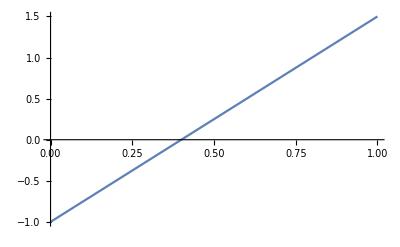

```mathematica
Plot[Sinh[(x-.4) 0.001]/Sinh[0.0010.4],{x,0,1}]
```